```mathematica
Exp[-({1/2,1/2,0}]
```

```mathematica
{1/2,1/2,0}
```

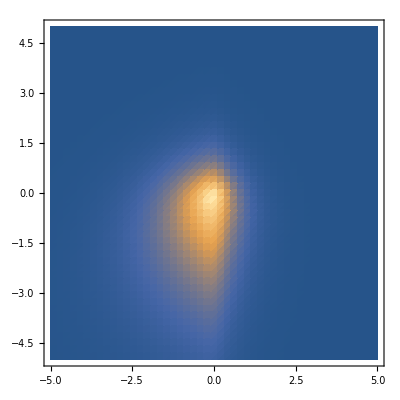

```mathematica
DensityPlot[Exp[-√(r1.r1-Abs[r1.Normalize[{1/(√2),1/(√2),0}]]^2)]Exp[-√(r.r-Abs[r.{1/(√2),-1/(√2),0}]^2)]Exp[-√(r.r-Abs[r.{0,0,1}]^2)]/.r1->{x+20,0,z+10}/.r->{x,0,z},{x,-5,5},{z,-5,5},PlotPoints->50,PlotRange->All]
```

```mathematica
0.9^8
```

0.430467

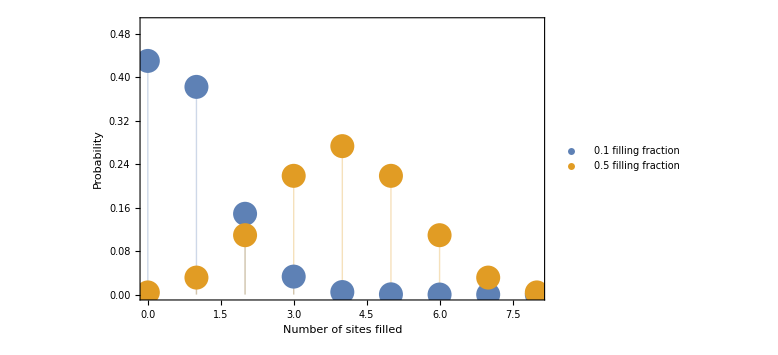

```mathematica
ListPlot[With[{nTot=8},Table[{n,p^n(1-p)^(nTot-n)Binomial[nTot,n]},{n,0,8},{p,{0.1,0.5}}]]ᵀ,Filling->Axis,PlotRange->{0,.5},PlotStyle->PointSize[.03],FrameLabel->{"Number of sites filled","Probability"},PlotLegends->{"0.1 filling fraction","0.5 filling fraction"},BaseStyle->FontSize->15,ImageSize->Large,Frame->True]
```